```mathematica
n=64;dx=1.0/(n-1.);
Courant=1/(√2);
dt=(Courant dx)/c;c=1.;
iter=Compile[{{tf,_Real}},Module[{z1=ConstantArray[0.,{64,64}],z2=ConstantArray[0.,{64,64}]},Do[{z1,z2}={z2,z1};z1⟦32,16⟧=Sin[16. π t];Do[If[0.45<i/n<0.55||!0.48<j/n<0.52,z2⟦i,j⟧=1/(1.+5. dt)(Courant^2 (z1⟦i-1,j⟧+z1⟦i+1,j⟧+z1⟦i,j-1⟧+z1⟦i,j+1⟧))-z2⟦i,j⟧],{i,2,63},{j,2,63}],{t,0.,tf,dt}];z1]]
```

CompiledFunction[…]

```mathematica
ripple=iter[0.45];
```

```mathematica
ListPlot3D[iter[1],Mesh->False,PlotRange->{-1,1},ImageSize->450,ColorFunction->"DeepSeaColors"]
```

-Graphics3D-

```mathematica
Head[ripple]
```

List

```mathematica
Dimensions[ripple]
```

{64,64}

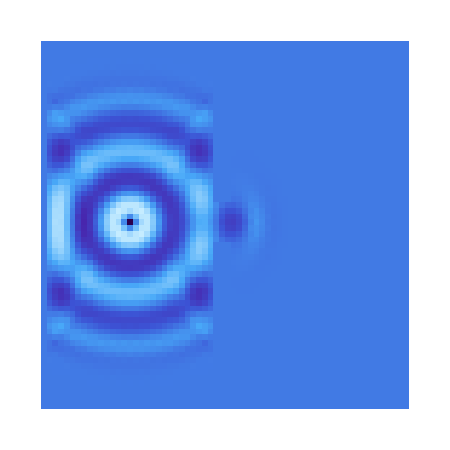

```mathematica
ArrayPlot[ripple,Frame->False,Mesh->False,ColorFunction -> "DeepSeaColors",ImageSize->450]
```